## Log[p]

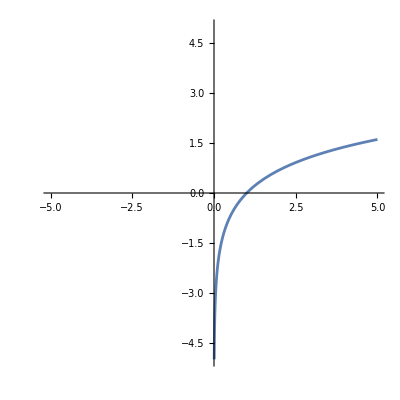

```mathematica
Plot[
Log[p],
{p,-5,5},
PlotRange->5,
AspectRatio->1
]
```

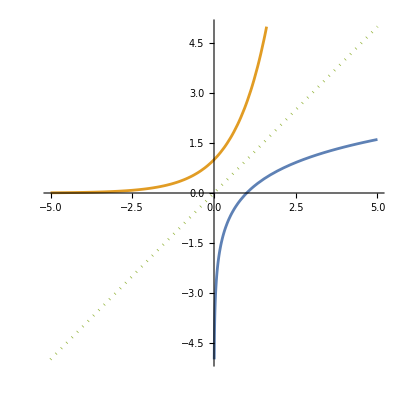

```mathematica
Plot[{Log[p],Exp[p],p},{p,-5,5},PlotRange->5,PlotStyle->{Automatic,Automatic,Dotted},AspectRatio->1]
```

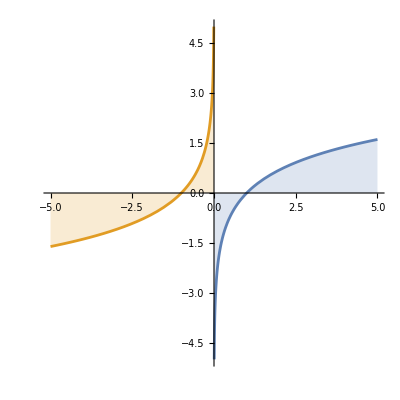

```mathematica
Plot[
{
Log[p],
-Log[-p]
},
{p,-5,5},
PlotRange->5,
AspectRatio->1,
Filling->0
]
```

```mathematica
Limit[Log[p],p->0]
```

-∞

## Shannon Entropy

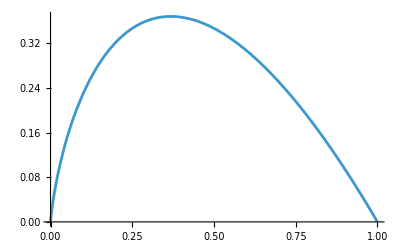

```mathematica
Plot[-x*Log[x],{x,0,1}]
```

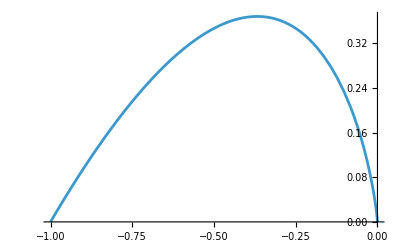

```mathematica
Plot[x*Log[-x],{x,-1,0}]
```

## Pythagoras

```mathematica
Manipulate[
c=Sqrt[a^2+b^2];
bx=b^2/c;
ax=a^2/c;
pointA={0,0};
pointB={b,a};
pointC={b,0};
pointX={b,a}/(a^2+b^2)*b^2;
pointY=pointX+{-a,b};
Graphics[{EdgeForm[Black],
{GrayLevel[.9],Triangle[{{0,0},{b,0},{b,a}}]},
{GrayLevel[.5],Rectangle[{0,-b},{b,0}]},
{GrayLevel[.7],Rectangle[{b,0},{b+a,a}]},
{GrayLevel[.7],Polygon[{{0,0},{b,a},{b-a,b+a},{-a,b}}]},
{GrayLevel[.5],Polygon[{{0,0},pointX,pointY,{-a,b}}]},
{Black,Line[{{b,0},pointX}]},
{Text["b^2",{b/2,-b/2}],
Text["b^2",pointY/2],
Text["a^2",{b+a/2,a/2}],
Text["a^2",(pointX+{b-a,b+a})/2],
Text["Δ",(pointX+{b,0})/2,{1,1}],
Text[UnderBar["x"],(pointX+{0,0})/2,{0,1}],
Text["x",(pointX+{b,a})/2,{0,1}]
}
}
],
{{a,1},0,2},
{{b,1},0,2},
{c,None},
{bx,None},
{ax,None},
{pointA,None},
{pointB,None},
{pointC,None},
{pointX,None},
{pointY,None}
]
```

## Photon Clock

```mathematica
Manipulate[
Graphics[{
{Dotted,Line[{{0,0},{0,-a*eventCount}}]},
{Dotted,Line[{{d,0},{d,-a*eventCount}}]},

{GrayLevel[.5],Table[Text["a",{0,-a*eventNumber-a/2},{2,0}],{eventNumber,0,eventCount-1}]},
{GrayLevel[.5],Table[Text["b",{d,-a*eventNumber+a/2},{-2,0}],{eventNumber,1,eventCount}]},
{GrayLevel[.3],Table[Text["c",{d/2,-a*eventNumber+a/2},{0,-1.5}],{eventNumber,1,eventCount}]},
,
If[showΔ,
{GrayLevel[.7],
Table[Line[{{0,-a}+{0,-a*eventNumber},{(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{eventNumber,0,eventCount-1,2}],
Table[Text["Δ",Mean[{{0,-a}+{0,-a*eventNumber},{(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{-2,0}],{eventNumber,0,eventCount-1,2}],
Table[Text["x",Mean[{{0,0}+{0,-a*eventNumber},{(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{0,1}],{eventNumber,0,eventCount-1,2}],
Table[Text[UnderBar["x"],Mean[{{d,-a}+{0,-a*eventNumber},{(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{0,1}],{eventNumber,0,eventCount-1,2}],


Table[Line[{{d,-a}+{0,-a*eventNumber},{d-(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{eventNumber,1,eventCount-1,2}],
Table[Text["Δ",Mean[{{d,-a}+{0,-a*eventNumber},{d-(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{2,0}],{eventNumber,1,eventCount-1,2}],
Table[Text["x",Mean[{{d,0}+{0,-a*eventNumber},{d-(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{0,1}],{eventNumber,1,eventCount-1,2}],
Table[Text[UnderBar["x"],Mean[{{0,-a}+{0,-a*eventNumber},{d-(a^2 d)/(a^2+d^2),-a^3/(a^2+d^2)}+{0,-a*eventNumber}}],{0,1}],{eventNumber,1,eventCount-1,2}]
}],

{GrayLevel[.6],
Table[Line[{{0,-a*eventNumber},{d,-a*eventNumber}}],{eventNumber,1,eventCount}]
},

{FaceForm[GrayLevel[.7]],EdgeForm[Black],
Table[Disk[{Mod[eventNumber,2]*d,-eventNumber*a},.1],{eventNumber,0,eventCount}]
},

{FaceForm[Black],
Table[Disk[{0,-a*eventNumber},.05],{eventNumber,1,eventCount,2}],
Table[Disk[{d,-a*eventNumber},.05],{eventNumber,0,eventCount,2}]
},

{GrayLevel[.3],Arrowheads[.1*arrowSize],
If[reverseArrows==True,
Table[Arrow[Reverse@{{Mod[eventNumber,2]*d,-eventNumber*a},{Mod[eventNumber+1,2]*d,-a*(eventNumber+1)}},.1],{eventNumber,0,eventCount-1}],
Table[Arrow[{{Mod[eventNumber,2]*d,-eventNumber*a},{Mod[eventNumber+1,2]*d,-a*(eventNumber+1)}},.1],{eventNumber,0,eventCount-1}]
]
}
}
]
,{{eventCount,5},1,10,1}
,{{a,1.},0,5}
,{{d,1.},0,5}
,{{arrowSize,1},0,5}
,{{reverseArrows,False},{True,False}}
,{{showΔ,True},{True,False}}
]
```